```mathematica
S[r_]:=Which[Abs[r]≤ 0.5,(1+(1-3 r^2)^(1/2))/3,0.5<Abs[r]≤1.5,(5-3*Abs[r]-(-3*(1-Abs[r])*(1-Abs[r])+1)^(1/2))/6, Abs[r] ≥ 1.5,0]
```

```mathematica
NIntegrate[S[rx]S[ry]S[rz],{rx,-1.5,1.5},{ry,-1.5,1.5},{rz,-1.5,1.5}]
```

1.

```mathematica
ContourPlot3D[S[r1]S[r2]S[r3]==0.1,{r1,-1.5,1.5},{r2,-1.5,1.5},{r3,-1.5,1.5}]
```

-Graphics3D-

```mathematica
dx=1;
pos={3.1,2.89,2.2};
grid=Flatten[Table[{ii*dx,jj*dx,kk*dx},{ii,0,5},{jj,0,5},{kk,0,5}],2]
w=Table[S[-grid[[ii,1]]+pos[[1]]]S[-grid[[ii,2]]+pos[[2]]]S[-grid[[ii,3]]+pos[[3]]],{ii,1,Length[grid]}]
Total[w]
```

{{0,0,0},{0,0,1},{0,0,2},{0,0,3},{0,0,4},{0,0,5},{0,1,0},{0,1,1},{0,1,2},{0,1,3},{0,1,4},{0,1,5},{0,2,0},{0,2,1},{0,2,2},{0,2,3},{0,2,4},{0,2,5},{0,3,0},{0,3,1},{0,3,2},{0,3,3},{0,3,4},{0,3,5},{0,4,0},{0,4,1},{0,4,2},{0,4,3},{0,4,4},{0,4,5},{0,5,0},{0,5,1},{0,5,2},{0,5,3},{0,5,4},{0,5,5},{1,0,0},{1,0,1},{1,0,2},{1,0,3},{1,0,4},{1,0,5},{1,1,0},{1,1,1},{1,1,2},{1,1,3},{1,1,4},{1,1,5},{1,2,0},{1,2,1},{1,2,2},{1,2,3},{1,2,4},{1,2,5},{1,3,0},{1,3,1},{1,3,2},{1,3,3},{1,3,4},{1,3,5},{1,4,0},{1,4,1},{1,4,2},{1,4,3},{1,4,4},{1,4,5},{1,5,0},{1,5,1},{1,5,2},{1,5,3},{1,5,4},{1,5,5},{2,0,0},{2,0,1},{2,0,2},{2,0,3},{2,0,4},{2,0,5},{2,1,0},{2,1,1},{2,1,2},{2,1,3},{2,1,4},{2,1,5},{2,2,0},{2,2,1},{2,2,2},{2,2,3},{2,2,4},{2,2,5},{2,3,0},{2,3,1},{2,3,2},{2,3,3},{2,3,4},{2,3,5},{2,4,0},{2,4,1},{2,4,2},{2,4,3},{2,4,4},{2,4,5},{2,5,0},{2,5,1},{2,5,2},{2,5,3},{2,5,4},{2,5,5},{3,0,0},{3,0,1},{3,0,2},{3,0,3},{3,0,4},{3,0,5},{3,1,0},{3,1,1},{3,1,2},{3,1,3},{3,1,4},{3,1,5},{3,2,0},{3,2,1},{3,2,2},{3,2,3},{3,2,4},{3,2,5},{3,3,0},{3,3,1},{3,3,2},{3,3,3},{3,3,4},{3,3,5},{3,4,0},{3,4,1},{3,4,2},{3,4,3},{3,4,4},{3,4,5},{3,5,0},{3,5,1},{3,5,2},{3,5,3},{3,5,4},{3,5,5},{4,0,0},{4,0,1},{4,0,2},{4,0,3},{4,0,4},{4,0,5},{4,1,0},{4,1,1},{4,1,2},{4,1,3},{4,1,4},{4,1,5},{4,2,0},{4,2,1},{4,2,2},{4,2,3},{4,2,4},{4,2,5},{4,3,0},{4,3,1},{4,3,2},{4,3,3},{4,3,4},{4,3,5},{4,4,0},{4,4,1},{4,4,2},{4,4,3},{4,4,4},{4,4,5},{4,5,0},{4,5,1},{4,5,2},{4,5,3},{4,5,4},{4,5,5},{5,0,0},{5,0,1},{5,0,2},{5,0,3},{5,0,4},{5,0,5},{5,1,0},{5,1,1},{5,1,2},{5,1,3},{5,1,4},{5,1,5},{5,2,0},{5,2,1},{5,2,2},{5,2,3},{5,2,4},{5,2,5},{5,3,0},{5,3,1},{5,3,2},{5,3,3},{5,3,4},{5,3,5},{5,4,0},{5,4,1},{5,4,2},{5,4,3},{5,4,4},{5,4,5},{5,5,0},{5,5,1},{5,5,2},{5,5,3},{5,5,4},{5,5,5}}

{0,0.,0.,0.,0,0,0,0.,0.,0.,0,0,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0,0.,0.,0.,0,0,0,0.,0.,0.,0,0,0,0.,0.,0.,0,0,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0,0.,0.,0.,0,0,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00206195,0.0173028,0.00741862,0.,0.,0.,0.00606107,0.0508614,0.021807,0.,0.,0.,0.00105263,0.0088331,0.00378721,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0114464,0.096052,0.0411826,0.,0.,0.,0.0336465,0.282344,0.121056,0.,0.,0.,0.00584339,0.0490347,0.0210237,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00379198,0.0318203,0.013643,0.,0.,0.,0.0111465,0.0935354,0.0401036,0.,0.,0.,0.00193581,0.0162443,0.00696479,0.,0.,0.,0.,0.,0.,0.,0.,0,0.,0.,0.,0,0,0,0.,0.,0.,0,0,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0,0.,0.,0.,0,0}

1.

```mathematica
S[0.3]S[0.3]S[0.3]
```

0.236182

```mathematica
Clear[sep]
r1abs=(x1^2+y1^2+z1^2)^(1/2);
r2abs=(x2^2+y2^2+z2^2)^(1/2);
r1vec={x1,y1,z1};
r2vec={x2,y2,z2};
rij={sep,0,0};
diff=r2vec-rij
diffabs=(diff[[1]]^2+diff[[2]]^2+diff[[3]]^2)^(1/2)
rad=r2vec-r1vec
radabs=(rad[[1]]^2+rad[[2]]^2+rad[[3]]^2)^(1/2)
```

{-sep+x2,y2,z2}

√((-sep+x2)^2+y2^2+z2^2)

{-x1+x2,-y1+y2,-z1+z2}

√((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2)

```mathematica
S[x1]S[y1]S[z1]S[diff[[1]]]S[diff[[2]]]S[diff[[3]]]((r2vec-r1vec)/radabs^3)[[1]]
```

1/(((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2)^(3/2))(-x1+x2) Which[Abs[x1]≤0.5,1/3 (1+√(1-3 x1^2)),0.5<Abs[x1]≤1.5,1/6 (5-3 Abs[x1]-√(-3 (1-Abs[x1]) (1-Abs[x1])+1)),Abs[x1]≥1.5,0] Which[Abs[-sep+x2]≤0.5,1/3 (1+√(1-3 (-sep+x2)^2)),0.5<Abs[-sep+x2]≤1.5,1/6 (5-3 Abs[-sep+x2]-√(-3 (1-Abs[-sep+x2]) (1-Abs[-sep+x2])+1)),Abs[-sep+x2]≥1.5,0] Which[Abs[y1]≤0.5,1/3 (1+√(1-3 y1^2)),0.5<Abs[y1]≤1.5,1/6 (5-3 Abs[y1]-√(-3 (1-Abs[y1]) (1-Abs[y1])+1)),Abs[y1]≥1.5,0] Which[Abs[y2]≤0.5,1/3 (1+√(1-3 y2^2)),0.5<Abs[y2]≤1.5,1/6 (5-3 Abs[y2]-√(-3 (1-Abs[y2]) (1-Abs[y2])+1)),Abs[y2]≥1.5,0] Which[Abs[z1]≤0.5,1/3 (1+√(1-3 z1^2)),0.5<Abs[z1]≤1.5,1/6 (5-3 Abs[z1]-√(-3 (1-Abs[z1]) (1-Abs[z1])+1)),Abs[z1]≥1.5,0] Which[Abs[z2]≤0.5,1/3 (1+√(1-3 z2^2)),0.5<Abs[z2]≤1.5,1/6 (5-3 Abs[z2]-√(-3 (1-Abs[z2]) (1-Abs[z2])+1)),Abs[z2]≥1.5,0]

```mathematica
dx=1.95*10^-7;
q=1.6*10^-19;
perm=8.85*10^-21;

pf=q^2/(perm 4 π dx^2);
Clear[sep,ni]
ni[sep_]:=NIntegrate[1/(((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2)^(3/2))(-x1+x2) Which[Abs[x1]≤0.5,1/3 (1+√(1-3 x1^2)),0.5<Abs[x1]≤1.5,1/6 (5-3 Abs[x1]-√(-3 (1-Abs[x1]) (1-Abs[x1])+1)),Abs[x1]≥1.5,0] Which[Abs[-sep+x2]≤0.5,1/3 (1+√(1-3 (-sep+x2)^2)),0.5<Abs[-sep+x2]≤1.5,1/6 (5-3 Abs[-sep+x2]-√(-3 (1-Abs[-sep+x2]) (1-Abs[-sep+x2])+1)),Abs[-sep+x2]≥1.5,0] Which[Abs[y1]≤0.5,1/3 (1+√(1-3 y1^2)),0.5<Abs[y1]≤1.5,1/6 (5-3 Abs[y1]-√(-3 (1-Abs[y1]) (1-Abs[y1])+1)),Abs[y1]≥1.5,0] Which[Abs[y2]≤0.5,1/3 (1+√(1-3 y2^2)),0.5<Abs[y2]≤1.5,1/6 (5-3 Abs[y2]-√(-3 (1-Abs[y2]) (1-Abs[y2])+1)),Abs[y2]≥1.5,0] Which[Abs[z1]≤0.5,1/3 (1+√(1-3 z1^2)),0.5<Abs[z1]≤1.5,1/6 (5-3 Abs[z1]-√(-3 (1-Abs[z1]) (1-Abs[z1])+1)),Abs[z1]≥1.5,0] Which[Abs[z2]≤0.5,1/3 (1+√(1-3 z2^2)),0.5<Abs[z2]≤1.5,1/6 (5-3 Abs[z2]-√(-3 (1-Abs[z2]) (1-Abs[z2])+1)),Abs[z2]≥1.5,0],{x1,-1.5,1.5},{x2,sep-1.5,sep+1.5},{y1,-1.5,1.5},{y2,-1.5,1.5},{z1,-1.5,1.5},{z2,-1.5,1.5},Method->"MonteCarlo",MaxPoints->500000]
```

```mathematica
samp=10;
points=20;
delr=4/points;
smeared=Table[{jj*delr,Total[Table[ni[jj*delr],{ii,1,samp}]]/samp},{jj,1,points}]
```

NIntegrate::maxp: The integral failed to converge after 500100 integrand evaluations. NIntegrate obtained 0.104583 and 0.0173817 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 500100 integrand evaluations. NIntegrate obtained 0.134621 and 0.0265213 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 500100 integrand evaluations. NIntegrate obtained 0.145971 and 0.0273011 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

{{1/5,0.105455},{2/5,0.198365},{3/5,0.262199},{4/5,0.323164},{1,0.344058},{6/5,0.345569},{7/5,0.32854},{8/5,0.300173},{9/5,0.265824},{2,0.23133},{11/5,0.198858},{12/5,0.16997},{13/5,0.146287},{14/5,0.126345},{3,0.109835},{16/5,0.09688},{17/5,0.0861714},{18/5,0.0765387},{19/5,0.0691103},{4,0.0624085}}

6.05365×10^-6

```mathematica
poisson1=Reverse[{{4,4.11*10^-7},{3.6,5.24*10^-7},{3.2,6.89*10^-7},{2.8,9.10*10^-7},{2.4,1.20*10^-6},{2.0,1.60*10^-6},{1.6,1.91*10^-6},{1.2,1.91*10^-6},{0.8,1.61*10^-6},{0.4,9.95*10^-7}}]
smearedS=Table[{smeared[[ii,1]],pf*smeared[[ii,2]]},{ii,1,points}]
```

{{0.4,9.95×10^-7},{0.8,1.61×10^-6},{1.2,1.91×10^-6},{1.6,1.91×10^-6},{2.,1.6×10^-6},{2.4,1.2×10^-6},{2.8,9.1×10^-7},{3.2,6.89×10^-7},{3.6,5.24×10^-7},{4,4.11×10^-7}}

{{1/5,6.38389×10^-7},{2/5,1.20083×10^-6},{3/5,1.58726×10^-6},{4/5,1.95632×10^-6},{1,2.08281×10^-6},{6/5,2.09195×10^-6},{7/5,1.98887×10^-6},{8/5,1.81714×10^-6},{9/5,1.60921×10^-6},{2,1.40039×10^-6},{11/5,1.20382×10^-6},{12/5,1.02894×10^-6},{13/5,8.85569×10^-7},{14/5,7.64848×10^-7},{3,6.64905×10^-7},{16/5,5.86478×10^-7},{17/5,5.21652×10^-7},{18/5,4.63339×10^-7},{19/5,4.1837×10^-7},{4,3.778×10^-7}}

```mathematica
correct=Table[{ii*delr,pf/(ii delr)^2},{ii,1,points}];
```

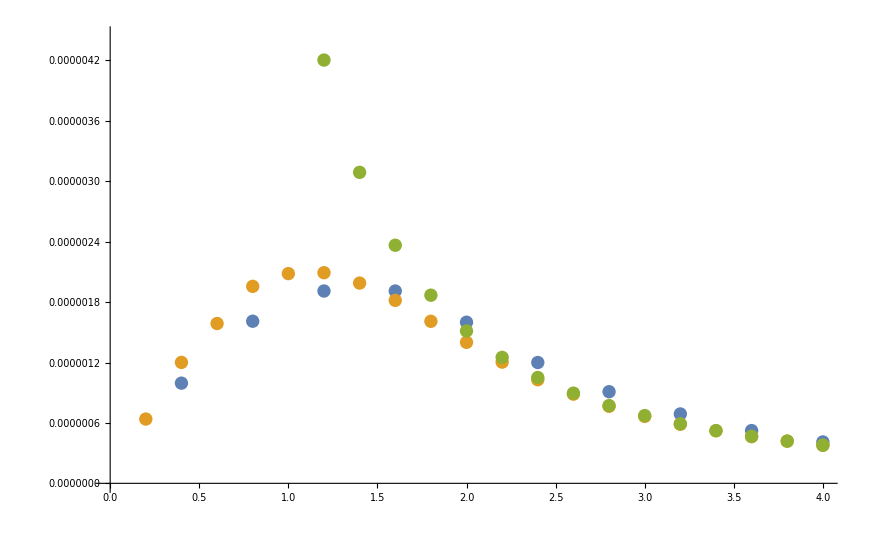

```mathematica
ListPlot[{poisson1,smearedS,correct}]
```

```mathematica
tab6={{0,0},{0.1,7.89*10^-8},{0.2,1.57*10^-7},
{0.3,2.33*10^-7},{0.4,3.07*10^-7},{0.5,3.78*10^-7},{0.6,4.45*10^-7},{0.7,5.07*10^-7},{0.8,5.64*10^-7},{0.9,6.17*10^-7},{1.0,6.63*10^-7},{1.1,7.04*10^-7},{1.2,7.37*10^-7},{1.3,7.66*10^-7},{1.4,7.89*10^-7},{1.5,8.05*10^-7},{1.6,8.12*10^-7},{1.7,8.21*10^-7},{1.8,8.19*10^-7},{1.9,8.15*10^-7},{2.0,8.07*10^-7},{2.1,7.93*10^-7},{2.2,7.83*10^-7},{2.3,7.64*10^-7},{2.4,7.39*10^-7},{2.5,7.16*10^-7},{2.6,6.97*10^-7},{2.7,6.70*10^-7},{2.8,6.45*10^-7},{2.9,6.22*10^-7},{3.0,5.93*10^-7},
{3.1,5.67*10^-7},{3.2,5.44*10^-7},{3.3,5.21*10^-7},{3.4,4.94*10^-7},{3.5,4.74*10^-7},{3.6,4.51*10^-7},{3.7,4.28*10^-7},
{3.8,4.12*10^-7},{3.9,3.91*10^-7},{4.0,3.73*10^-7},{4.1,3.55*10^-7},{4.2,3.40*10^-7},{4.3,3.24*10^-7},{4.4,3.11*10^-7},
{4.5,2.95*10^-7},{4.6,2.84*10^-7},{4.7,2.73*10^-7},{4.8,2.61*10^-7},{4.9,2.51*10^-7},{5.0,2.42*10^-7},{5.1,2.32*10^-7},
{5.2,2.22*10^-7},{5.3,2.15*10^-7},{5.4,2.06*10^-7},{5.5,1.99*10^-7},{5.6,1.92*10^-7},{5.7,1.86*10^-7},{5.8,1.79*10^-7},
{5.9,1.73*10^-7},{6.0,1.67*10^-7},{6.1,1.62*10^-7},{6.2,1.57*10^-7},{6.3,1.52*10^-7},{6.4,1.47*10^-7},{6.5,1.43*10^-7},
{6.6,1.39*10^-7},{6.7,1.34*10^-7},{6.8,1.30*10^-7},{6.9,1.27*10^-7}}
```

{{0,0},{0.1,7.89×10^-8},{0.2,1.57×10^-7},{0.3,2.33×10^-7},{0.4,3.07×10^-7},{0.5,3.78×10^-7},{0.6,4.45×10^-7},{0.7,5.07×10^-7},{0.8,5.64×10^-7},{0.9,6.17×10^-7},{1.,6.63×10^-7},{1.1,7.04×10^-7},{1.2,7.37×10^-7},{1.3,7.66×10^-7},{1.4,7.89×10^-7},{1.5,8.05×10^-7},{1.6,8.12×10^-7},{1.7,8.21×10^-7},{1.8,8.19×10^-7},{1.9,8.15×10^-7},{2.,8.07×10^-7},{2.1,7.93×10^-7},{2.2,7.83×10^-7},{2.3,7.64×10^-7},{2.4,7.39×10^-7},{2.5,7.16×10^-7},{2.6,6.97×10^-7},{2.7,6.7×10^-7},{2.8,6.45×10^-7},{2.9,6.22×10^-7},{3.,5.93×10^-7},{3.1,5.67×10^-7},{3.2,5.44×10^-7},{3.3,5.21×10^-7},{3.4,4.94×10^-7},{3.5,4.74×10^-7},{3.6,4.51×10^-7},{3.7,4.28×10^-7},{3.8,4.12×10^-7},{3.9,3.91×10^-7},{4.,3.73×10^-7},{4.1,3.55×10^-7},{4.2,3.4×10^-7},{4.3,3.24×10^-7},{4.4,3.11×10^-7},{4.5,2.95×10^-7},{4.6,2.84×10^-7},{4.7,2.73×10^-7},{4.8,2.61×10^-7},{4.9,2.51×10^-7},{5.,2.42×10^-7},{5.1,2.32×10^-7},{5.2,2.22×10^-7},{5.3,2.15×10^-7},{5.4,2.06×10^-7},{5.5,1.99×10^-7},{5.6,1.92×10^-7},{5.7,1.86×10^-7},{5.8,1.79×10^-7},{5.9,1.73×10^-7},{6.,1.67×10^-7},{6.1,1.62×10^-7},{6.2,1.57×10^-7},{6.3,1.52×10^-7},{6.4,1.47×10^-7},{6.5,1.43×10^-7},{6.6,1.39×10^-7},{6.7,1.34×10^-7},{6.8,1.3×10^-7},{6.9,1.27×10^-7}}

```mathematica
tab6[[All,1]]//TextString
```

{0, 0.1, 0.2, 0.3, 0.4, 0.5, 0.6, 0.7, 0.8, 0.9, 1., 1.1, 1.2, 1.3, 1.4, 1.5, 1.6, 1.7, 1.8, 1.9, 2., 2.1, 2.2, 2.3, 2.4, 2.5, 2.6, 2.7, 2.8, 2.9, 3., 3.1, 3.2, 3.3, 3.4, 3.5, 3.6, 3.7, 3.8, 3.9, 4., 4.1, 4.2, 4.3, 4.4, 4.5, 4.6, 4.7, 4.8, 4.9, 5., 5.1, 5.2, 5.3, 5.4, 5.5, 5.6, 5.7, 5.8, 5.9, 6., 6.1, 6.2, 6.3, 6.4, 6.5, 6.6, 6.7, 6.8, 6.9}

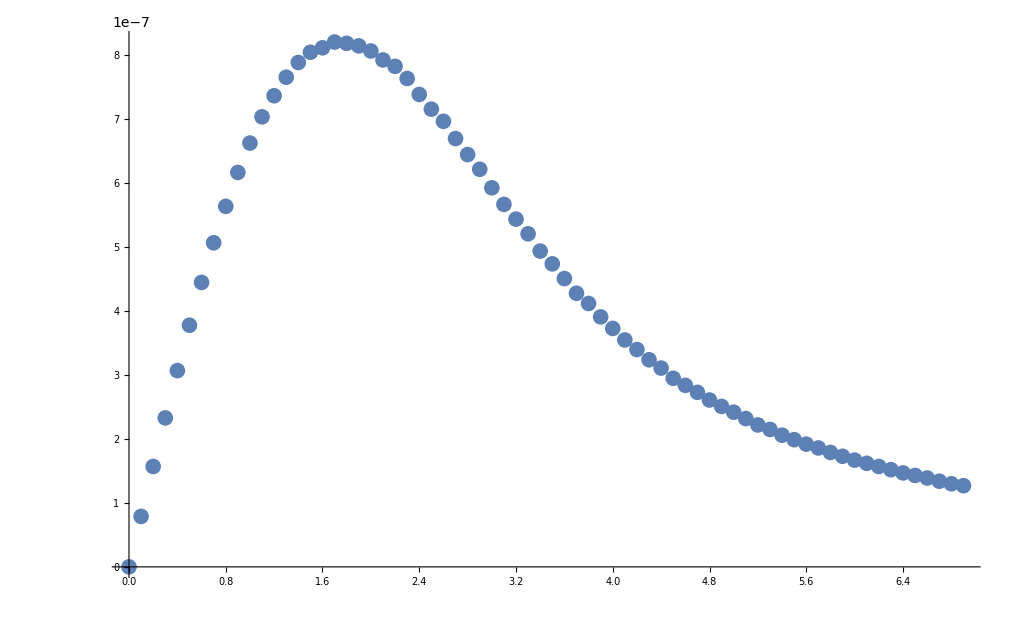

```mathematica
ListPlot[tab6]
```

```mathematica
Length[tab6]
```

70